## Evolution with Expansion to match unitaries

```mathematica
sigmax={{0,1},{1,0}};
sigmay={{0, -ⅈ},{ⅈ,0}};
id2=IdentityMatrix[2];
```

```mathematica
trueHam=KroneckerProduct[sigmax, sigmax];
trueHam//MatrixForm
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
simHamgood=KroneckerProduct[sigmax, id2];
simHambad=KroneckerProduct[sigmay, id2];
simHamgood//MatrixForm
simHambad//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)

```mathematica
rand1q[]:=RandomReal[]+ⅈ RandomReal[];
```

```mathematica
FindEvoLikelihood[Ham_,time_,probe_]:=N@Abs[((probe*).MatrixExp[-ⅈ Ham time].probe)^2];
```

```mathematica
testprobe=Normalize@Flatten@KroneckerProduct[{1,1},{1,1}];
N@FindEvoLikelihood[trueHam,25,testprobe]
```

1.

```mathematica
listHams={trueHam,simHamgood,simHambad};
```

{-0.376022+0.592319 ⅈ,-0.19645+0.312013 ⅈ,0.274547+0.464735 ⅈ,0.14519+0.243692 ⅈ}

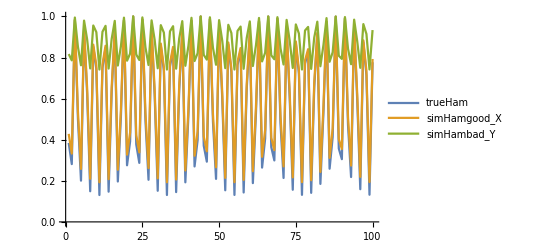

```mathematica
probe=Normalize@Flatten@KroneckerProduct[{rand1q[], rand1q[]}, {rand1q[], rand1q[]}]

AllEvos=ParallelTable[
Table[
FindEvoLikelihood[thisHam,time,probe],{time,1,100}],
{thisHam, listHams}];

ListLinePlot[Table[AllEvos⟦i,All⟧,{i,1,3}],PlotLegends->{"trueHam","simHamgood_X","simHambad_Y"}]
```

```mathematica
realprobe=Normalize@Flatten@KroneckerProduct[{RandomReal[], RandomReal[]}, {RandomReal[], RandomReal[]}]
```

{0.858956,0.292111,0.39816,0.135405}

```mathematica
AllEvos=ParallelTable[
Table[
FindEvoLikelihood[thisHam,time,realprobe],{time,1,100}],
{thisHam, listHams}];
```

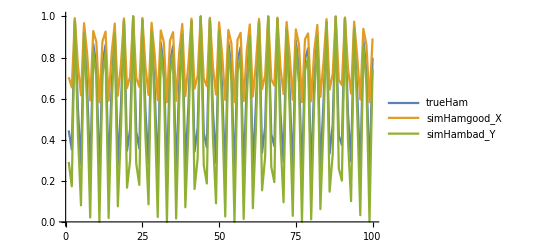

```mathematica
ListLinePlot[Table[AllEvos⟦i,All⟧,{i,1,3}],PlotLegends->{"trueHam","simHamgood_X","simHambad_Y"}]
```

## Evolution with PartialTrace to match output states

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

```mathematica
sigmax={{0,1},{1,0}};
sigmay={{0, -ⅈ},{ⅈ,0}};
id2=IdentityMatrix[2];
```

```mathematica
trueHam=KroneckerProduct[sigmax, sigmax];
trueHam//MatrixForm
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
simHamgood=sigmax;
simHambad=sigmay;
simHamgood//MatrixForm
simHambad//MatrixForm
```

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

```mathematica
rand1q[]:=RandomReal[]+ⅈ RandomReal[];
```

```mathematica
FindEvoLikelihood[Ham_,time_,probe_]:=N@Abs[((probe*).MatrixExp[-ⅈ Ham time].probe)^2];
```

```mathematica
(probeDM=TraceSystem[KroneckerProduct[probe*,probe],{2}])//MatrixForm
```

(0.276657+0. ⅈ | 0.299272-0.332497 ⅈ
0.299272+0.332497 ⅈ | 0.723343+0. ⅈ)

```mathematica
evostate=MatrixExp[-ⅈ trueHam 0.0001].probe;
DM=KroneckerProduct[evostate*,evostate];
(redDM=TraceSystem[DM,{2}])//MatrixForm
fid=1-Chop@Tr@Abs[redDM-probeDM]
```

(0.276591+0. ⅈ | 0.299272-0.332452 ⅈ
0.299272+0.332452 ⅈ | 0.723409+0. ⅈ)

0.999867

```mathematica
FindRedLikelihood[Ham_,time_,probe_]:=Module[{evostate,DM,redDM,fid},
evostate=MatrixExp[-ⅈ trueHam time].probe;
DM=KroneckerProduct[evostate*,evostate];
redDM=TraceSystem[DM,{2}];
fid=1-Chop@Tr@Abs[redDM-probeDM];
Return[fid]
]
```

```mathematica
FindRedLikelihood[trueHam,0.0001,probe]
```

-0.135382

{-0.579895+0.413202 ⅈ,0.0503778+0.397181 ⅈ,-0.453855+0.216322 ⅈ,-0.013607+0.282365 ⅈ}

{-0.709884+0.505825 ⅈ,0.0616704+0.486212 ⅈ}

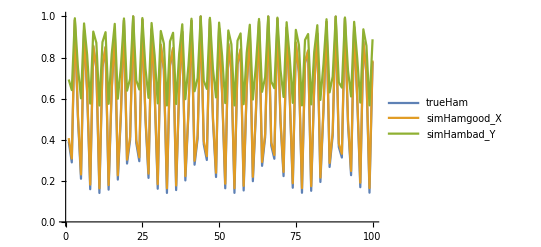

```mathematica
probe=Normalize@Flatten@KroneckerProduct[{rand1q[], rand1q[]}, {rand1q[], rand1q[]}]
smallprobe=Normalize[probe⟦1;;2⟧]

listHams={simHamgood,simHambad};
AllEvos=ParallelTable[
Table[
FindEvoLikelihood[thisHam,time,smallprobe],{time,1,100}],
{thisHam, listHams}];

RedEvos=ParallelTable[
FindEvoLikelihood[trueHam,time,probe],{time,1,100}];

ListLinePlot[{RedEvos,AllEvos⟦1,All⟧,AllEvos⟦2,All⟧},PlotLegends->{"trueHam","simHamgood_X","simHambad_Y"}]
```